# Coupled square well scattering and bound states

## A “simple” multichannel model

## 1-channel square well

As a preliminary to the multichannel case, we will need to solve the single channel case to understand where the bound states are with respect to the threshold.  This will help us interpret the two-channel resonances, at least in the weak coupling regime.  Inside the well of range r_0, the wavefunction satisfies:

(∂^2/(∂r^2)+(2μ)/ℏ^2(E+V_0)-(L(L+1))/r^2)r ψ=0

Let k^2=(2μ r_0^2 E)/ℏ^2 and γ^2=(2μ r_0^2 V_0)/ℏ^2.  Also RESCALE r→r/r_0.  Then

(∂^2/(∂r^2)+k^2+γ^2-(L(L+1))/r^2)r ψ=0

Let β^2=k^2+γ^2, and divide through by β^2

(∂^2/(∂(β r)^2)+1-(L(L+1))/(β r)^2)r ψ=0

The fundamental unit of length is r_0, the unit of energy is ℏ^2/(2μ r_0^2).

Then inside,

rψ_in(β r)= r j_l(β r)

Outside,

rψ_out(k r)= r k_l(κ r)

with κ^2=-2μ E/ℏ^2.  or.

ψ_in=j_l(β r)

ψ_out=k_l(κ r)

matching the log-derivatives gives:

```mathematica
Clear[V0]
```

```mathematica
SphericalBesselK[L_,z_]:=√(π/(2z))BesselK[L+1/2,z]
```

```mathematica
TEQ0=FullSimplify[D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r]/.{L->0,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]
```

√-EE+√(EE+V0) Cot[√(EE+V0)]

Let’s make this easier to handle by multiplying through by sin(√(E+V_0)) (it’s all equal to zero anyhow, so this doesn’t change the position of the roots.)

For s-waves:

```mathematica
TEQ0=FullSimplify[Sin[√(EE+V0)](D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->0,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]
```

√(EE+V0) Cos[√(EE+V0)]+√-EE Sin[√(EE+V0)]

for p-waves:

```mathematica
TEQ1=FullSimplify[FunctionExpand[(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->1,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

-(√(EE+V0) (EE √(EE+V0) Cos[√(EE+V0)]+(V0+√-EE (EE+V0)) Sin[√(EE+V0)]))/((1+√-EE) ((EE+V0) Cos[√(EE+V0)]-√(EE+V0) Sin[√(EE+V0)]))

```mathematica
TEQ1=FullSimplify[FunctionExpand[(1+√-EE) ((EE+V0) Cos[√(EE+V0)]-√(EE+V0) Sin[√(EE+V0)])(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->1,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

-√(EE+V0) (EE √(EE+V0) Cos[√(EE+V0)]+(V0+√-EE (EE+V0)) Sin[√(EE+V0)])

and for d-waves:

```mathematica
TEQ2=FullSimplify[FunctionExpand[(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->2,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

(√(EE+V0) ((-EE)^(5/2)-3 √-EE V0+(3+√-EE) EE V0) Cos[√(EE+V0)]-(EE^3-3 √-EE V0+EE (3+EE) V0) Sin[√(EE+V0)])/((-3 √-EE+(3+√-EE) EE) (3 √(EE+V0) Cos[√(EE+V0)]+(-3+EE+V0) Sin[√(EE+V0)]))

```mathematica
TEQ2=FullSimplify[FunctionExpand[((-3 √-EE+(3+√-EE) EE) (3 √(EE+V0) Cos[√(EE+V0)]+(-3+EE+V0) Sin[√(EE+V0)]))(D[Log[SphericalBesselJ[L,β r]],r]-D[Log[SphericalBesselK[L,κ r]],r])/.{L->2,r->1,β->√(EE+V0),k->√EE,κ->√-EE}]]
```

√(EE+V0) ((-EE)^(5/2)-3 √-EE V0+(3+√-EE) EE V0) Cos[√(EE+V0)]-(EE^3-3 √-EE V0+EE (3+EE) V0) Sin[√(EE+V0)]

For purposes of rootfinding, we’ll need to make a guess as to where the roots are.  Since we know the solutions in the interior region are simply besselfunctions, we can find approximate positions of the roots by treating the finite well like an infinite well and using the known zeroes of the Bessel function.  The additional “fudge factor” of (π/4 n)^2 seems to work well in correcting the high-lying states.

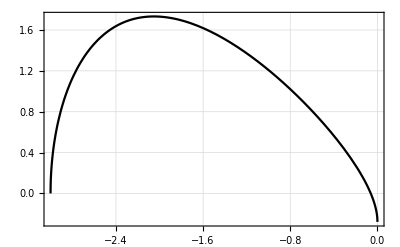

```mathematica
Vmax=3;
rootguess0=Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess0,PlotStyle->Green];
p3=Plot[√(EE+V0) Cos[√(EE+V0)]+√-EE Sin[√(EE+V0)]/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

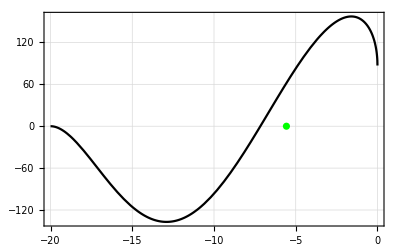

```mathematica
Vmax=20;
rootguess1=Table[{-Vmax+N[BesselJZero[3/2,n]]^2-(2.4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess1,PlotStyle->Green];
p3=Plot[TEQ1/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

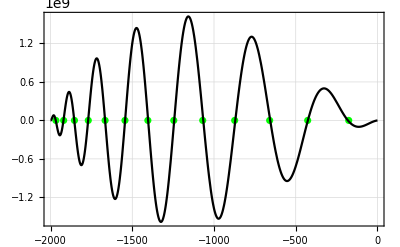

```mathematica
Vmax=2000;
rootguess2=Table[{-Vmax+N[BesselJZero[5/2,n]]^2-(π/4 n)^2,0},{n,1,20}];
p2=ListPlot[rootguess2,PlotStyle->Green];
p3=Plot[TEQ2/.V0->Vmax,{EE,-Vmax,0},PlotStyle->Black];Show[{p2,p3},PlotRange->{{-Vmax,0},All},Frame->True,GridLines->Automatic]
```

```mathematica
rootguess0=Select[Table[{-Vmax+N[BesselJZero[1/2,n]]^2-(π/4 n)^2,0},{n,1,50}],#[[1]]<100&]
```

{{-1990.75,0},{-1962.99,0},{-1916.73,0},{-1851.96,0},{-1768.68,0},{-1666.9,0},{-1546.62,0},{-1407.82,0},{-1250.53,0},{-1074.72,0},{-880.417,0},{-667.603,0},{-436.285,0},{-186.46,0},{81.8697,0}}

It’s also very helpful to know when there is a state at threshold.  So for what V_0 is the energy zero?

```mathematica
V0roots0=Sort[DeleteDuplicates[Table[V0/.FindRoot[TEQ0/.EE->0,{V0,Vn}],{Vn,2,Vmax,1}],(Abs[#1-#2]<10^-4&)]]
```

{9.13194×10^-22+0. ⅈ,2.4674,22.2066,61.685,120.903,199.859,298.556,416.991,555.165,713.079,890.732,1088.12,1305.26,1542.13,1798.74,2075.08,2371.17,2687.,3022.57,3377.87,4147.7,4562.22,4996.49,6417.71,6930.93,8016.59}

```mathematica
V0roots0Table=Table[{V0roots0[[n]],0},{n,1,Length[V0roots0]}]
```

{{9.13194×10^-22+0. ⅈ,0},{2.4674,0},{22.2066,0},{61.685,0},{120.903,0},{199.859,0},{298.556,0},{416.991,0},{555.165,0},{713.079,0},{890.732,0},{1088.12,0},{1305.26,0},{1542.13,0},{1798.74,0},{2075.08,0},{2371.17,0},{2687.,0},{3022.57,0},{3377.87,0},{4147.7,0},{4562.22,0},{4996.49,0},{6417.71,0},{6930.93,0},{8016.59,0}}

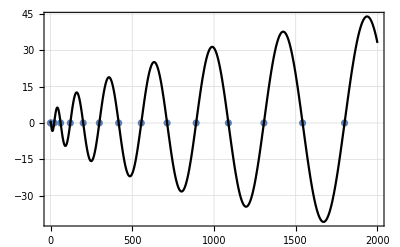

```mathematica
pv0=ListPlot[V0roots0Table];p0=Plot[TEQ0/.{EE->0},{V0,0,Vmax},PlotStyle->Black];Show[{pv0,p0},PlotRange->{{0,Vmax},All},Frame->True,GridLines->Automatic]
```

```mathematica
V0roots0[[2]]
```

2.4674

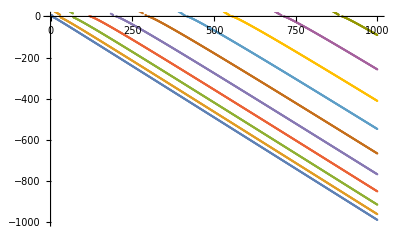

```mathematica
Vmax=1000;ListPlot[Table[{VV,EE/.FindRoot[TEQ0/.V0->VV,{EE,-VV+N[BesselJZero[1/2,n]]^2-(π/4 n)^2}]},{n,1,10},{VV,2.5,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

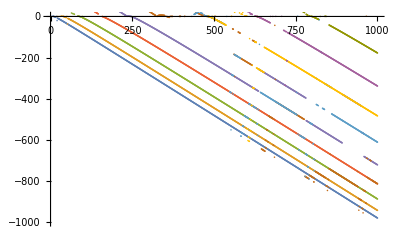

```mathematica
Vmax=1000;ListPlot[Table[{VV,EE/.FindRoot[TEQ1/.V0->VV,{EE,-VV+N[BesselJZero[3/2,n]]^2-(π/2 n)^2}]},{n,1,10},{VV,3,Vmax}],PlotRange->{{0,Vmax},{-Vmax,0}}]
```

```mathematica
DSolve[D[D[rψ[r],r],r]+k^2 rψ[r]-(L(L+1))/r^2 rψ[r]==0,rψ[r],r]
```

{{rψ[r]→√r BesselJ[1/2 (1+2 L),k r] C[1]+√r BesselY[1/2 (1+2 L),k r] C[2]}}

This is proportional to a spherical bessel funtion:

```mathematica
FullSimplify[FunctionExpand[{ρ SphericalBesselJ[L,k ρ],ρ SphericalBesselY[L,k ρ]}]]
```

{(√(π/2) ρ BesselJ[1/2+L,k ρ])/(√(k ρ)),(√(π/2) ρ BesselY[1/2+L,k ρ])/(√(k ρ))}

Here, r is measured in units of r_0, the well width.  k is measured in units of r_0^-1.

The solution that is regular at the origin is

r ψ^I=r j_L(√(k^2+γ^2)r)

For bound states, E<0.  Let κ^2=-k^2.  The solution in the exterior region is

```mathematica
TraditionalForm[FunctionExpand[DSolve[D[D[rψ[r],r],r]-κ^2 rψ[r]-(L(L+1))/r^2 rψ[r]==0,rψ[r],r,Assumptions->κ∈Reals ]]]
```

{{rψ(r)→-ⅈ κ r^(3/2) (κ r)^(-L-1/2) (-ⅈ κ r)^(-L-1/2) 1/2 (2 L+1)r κ (c_1 (-ⅈ κ r)^(2 L)+c_2 cot(1/2 π (2 L+1)) (-ⅈ κ r)^(2 L)-ⅈ c_2 csc(1/2 π (2 L+1)) (κ r)^(2 L))-(2 c_2 √r (κ r)^(L+1/2) (-ⅈ κ r)^(-L-1/2) 1/2 (2 L+1)r κ)/π}}

The part that is regular as r→∞ is the K_(L+1/2) piece.  The I_(L+1/2) blows up as r→∞.  We have

r ψ^II∝  √r  (-ⅈ )^(-L-1/2) 1/2 (2 L+1)r κ∝√r (-ⅈ)^L 1/2 (2 L+1)r κ

```mathematica
FullSimplify[Normal[Series[√r(-ⅈ )^(-L-1/2)BesselK[L+1/2,κ r],{r,DirectedInfinity[1],0}]],{κ>0,L∈Integers,L≥0}]
```

((1/2+ⅈ/2) ⅈ^L ⅇ^(-r κ) √π)/(√κ)

```mathematica
FullSimplify[-D[D[√r BesselK[L+1/2,κ r],r],r]-(-κ^2 √r BesselK[L+1/2,κ r]-(L(L+1))/r^2 √r BesselK[L+1/2,κ r])]
```

0

```mathematica
FullSimplify[√r(-ⅈ)^(-L-1/2)BesselK[L+1/2,κ r],Assumptions->{κ>0,r>0}]
```

(-ⅈ)^(-1/2-L) √r BesselK[1/2+L,r κ]

## 2-channel model

Before attempting the N-channel problem, let’s see if we can understand the 2-channel problem.  Consider a two-particle problem with the following Schrodinger equation for the radial wavefunction.

(-ℏ^2/(2μ)∂^2/(∂r^2)+V_1(r)+(ℏ^2 L(L+1))/(2μ r^2) | V_12
V_12 | -ℏ^2/(2μ)∂^2/(∂r^2)+V_2(r)+(ℏ^2 L(L+1))/(2μ r^2))( r ψ_1
 r ψ_2)=E (r ψ_1
r ψ_2)

Choose:

V_1(r)={-V_1
0         for  r<r_0
for r>r_0

V_2(r)={E_2^th-V_2
E_2^th      for  r<r_0
for r>r_0

Assume the off-diagonal coupling to be real (I think this is without loss of any generality since we’re solving a time-independent problem anyhow).

V_12(r)={V_12
0      for  r<r_0
for r>r_0

In region I (interior r<r_0)

(-ℏ^2/(2μ)∂^2/(∂r^2)-(V_1+E)+(ℏ^2 L(L+1))/(2μ r^2) | V_12
V_12 | -ℏ^2/(2μ)∂^2/(∂r^2)-(V_2-E_2^th+E)+(ℏ^2 L(L+1))/(2μ r^2))( r ψ_1^I
 r ψ_2^I)=0

Multiply through by 2μ/ℏ^2,

(-∂^2/(∂r^2)-(2μ)/ℏ^2(V_1+E)+(L(L+1))/r^2 | (2μ)/ℏ^2 V_12
(2μ)/ℏ^2 V_12 | -∂^2/(∂r^2)-(2μ)/ℏ^2(V_2-E_2^th+E)+(L(L+1))/r^2)(r ψ_1^I
r ψ_2^I)=0

We wish to measure length in units of r_0, and energy in units of ℏ^2/(2μ r_0^2), so we multiply through by r_0^2, and redefine r→ r/r_0:

(∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(V_1+E)-(L(L+1))/r^2 | (2μ r_0^2)/ℏ^2 V_12
(2μ r_0^2)/ℏ^2 V_12* | ∂^2/(∂r^2)+(2μ r_0^2)/ℏ^2(V_2-E_2^th+E)-(L(L+1))/r^2)(r ψ_1^I
r ψ_2^I)=0

Now note that for the scattering problem E>0.  By definition, V_i>0 ∀i and also, E_i^th>0 ∀i.

Let’s define

g=(2μ r_0^2)/ℏ^2 V_12  is a dimensionless coupling,

v_i= γ_i^2=(2μ r_0^2)/ℏ^2 V_i>0  is a wavenumber (squared) that measures the depth of the well in channel i,

ϵ=k^2=(2μ r_0^2)/ℏ^2 E  is the wavenumber in the asymptotic region of the open channel,

ϵ_i=ν_i^2=(2μ r_0^2)/ℏ^2 E_i^th>0  is a wavenumber (squared) measuring the threshold energy of channel i.

(∂^2/(∂r^2)+(ϵ+v_1)-(L(L+1))/ρ^2 | g
g | ∂^2/(∂ρ^2)+(ϵ+v_2-ϵ_2)-(L(L+1))/r^2)(r ψ_1^I
r ψ_2^I)=0

Write this as:

(∂^2/(∂r^2)+(ϵ+v_1)-(L(L+1))/ρ^2 | g
g | ∂^2/(∂ρ^2)+(ϵ+v_2-ϵ_2)-(L(L+1))/r^2)(r ψ_1^I
r ψ_2^I)=0

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+((ϵ+v_1) | g
g | (ϵ+v_2-ϵ_2))](r ψ_1^I
r ψ_2^I)=0

In the exterior region (II),  r>r_0, or ρ>1, we have:

[(∂^2/(∂r^2)-(L(L+1))/r^2 | 0
0 | ∂^2/(∂r^2)-(L(L+1))/r^2)+(ϵ | 0
0 | ϵ-ϵ_i)](ρψ_1^II
ρψ_2^II)=0

so the solutions in the exterior region where there is no coupling are (defining κ=√(ϵ-ϵ_i)):

r ψ^II=(r j_l(k r)
r k_l(κ r))

so we write

ρψ_1^II(r)=sin (k r)+K_L cos (k r)

ρψ_2^II(r)=ⅇ^(-κ r)     κ=√(ν_2^2-k^2)

```mathematica
Clear[k]
```

```mathematica
FullSimplify[FunctionExpand[{ρ SphericalBesselJ[L,k ρ],ρ SphericalBesselY[L,k ρ]}]]
```

{(√(π/2) ρ BesselJ[1/2+L,k ρ])/(√(k ρ)),(√(π/2) ρ BesselY[1/2+L,k ρ])/(√(k ρ))}

```mathematica
Simplify[DSolve[D[D[ρψ[ρ],ρ],ρ]-(L(L+1))/ρ^2 ρψ[ρ]+k^2 ρψ[ρ]==0,ρψ,ρ]]
```

{{ρψ→Function[{ρ},√ρ BesselJ[1/2 (1+2 L),k ρ] C[1]+√ρ BesselY[1/2 (1+2 L),k ρ] C[2]]}}

Evidently, ρψ_1^II must be a linear combination of ρ times a spherical Bessel functions.  i.e. that ψ goes as linear combination of spherical bessel functions.

ρψ_1^II=A_L ρ j_L(k ρ)+B_L ρ y_L(k ρ)

```mathematica
TraditionalForm[{k ρ SphericalBesselJ[ L,k ρ],k ρ SphericalBesselY[L,k ρ]}->Simplify[Normal[Series[{k ρ SphericalBesselJ[L,k ρ],k ρ SphericalBesselY[L,k ρ]},{ρ,DirectedInfinity[1],0}]],k>0]]
```

{k ρ Lk ρ,k ρ Lk ρ}→{(L (L+1) cos((π L)/2-k ρ)-2 k ρ sin((π L)/2-k ρ))/(2 k ρ),-(L (L+1) sin((π L)/2-k ρ)+2 k ρ cos((π L)/2-k ρ))/(2 k ρ)}

{k ρ Lk ρ,k ρ Lk ρ}→{ sin(k ρ-(π L)/2),- cos(k ρ-(π L)/2)}

So the asypm

In the interior region, the situation is more complicated due to the coupling.  It turns out that it is still possible to solve the problem exactly.  The trick is to use “dressed” states that are eigenstates of the constant matrix (assume g is real):

W=(k^2+γ_1^2 | g
g | k^2+γ_2^2-ν_2^2)

```mathematica
Clear[g,k]
```

```mathematica
W=({{k^2+Subscript[γ, 1]^2, g}, {g, k^2-Subscript[ν, 2]^2+Subscript[γ, 2]^2}})
```

{{k^2+γ_1^2,g},{g,k^2+γ_2^2-ν_2^2}}

```mathematica
Avecs=FullSimplify[Eigenvectors[W],Assumptions->{k∈Reals,Subscript[γ, 1]∈Reals,Subscript[γ, 2]∈Reals,Subscript[ν, 2]∈Reals,g∈Reals}]
```

{{(γ_1^2-γ_2^2+ν_2^2-√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))/(2 g),1},{(γ_1^2-γ_2^2+ν_2^2+√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))/(2 g),1}}

Define an orthogonal matrix comprised of normalized eigenvectors in the columns of the matrix.  Mathematica puts eigenvectors in the rows, so I’ll define this as the transpose of the output of “Eigenvectors” above:

```mathematica
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Avecs[[n]]],Assumptions->{k∈Reals,Subscript[γ, 1]∈Reals,Subscript[γ, 2]∈Reals,Subscript[ν, 2]∈Reals,g∈Reals}],{n,1,2}]]
```

{{(γ_1^2-γ_2^2+ν_2^2-√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))/(g √(4+((γ_1^2-γ_2^2+ν_2^2-√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))^2)/g^2)),(γ_1^2-γ_2^2+ν_2^2+√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))/(g √(4+((γ_1^2-γ_2^2+ν_2^2+√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))^2)/g^2))},{2/(√(4+((γ_1^2-γ_2^2+ν_2^2-√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))^2)/g^2)),2/(√(4+((γ_1^2-γ_2^2+ν_2^2+√(4 g^2+(γ_1^2-γ_2^2+ν_2^2)^2))^2)/g^2))}}

```mathematica
Avals=Simplify[Eigenvalues[W],Assumptions->{k∈Reals,Subscript[γ, 1]∈Reals,Subscript[γ, 2]∈Reals,Subscript[ν, 2]∈Reals,g∈Reals}]
```

{1/2 (2 k^2+γ_1^2+γ_2^2-ν_2^2-√(4 g^2+γ_1^4+γ_2^4-2 γ_2^2 ν_2^2+ν_2^4-2 γ_1^2 (γ_2^2-ν_2^2))),1/2 (2 k^2+γ_1^2+γ_2^2-ν_2^2+√(4 g^2+γ_1^4+γ_2^4-2 γ_2^2 ν_2^2+ν_2^4-2 γ_1^2 (γ_2^2-ν_2^2)))}

Let’s check that the matrix of eigenvectors is properly normalized:

```mathematica
MatrixForm[FullSimplify[AvecsNormed.AvecsNormedᵀ]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[FullSimplify[AvecsNormedᵀ.AvecsNormed]]
```

(1 | 0
0 | 1)

```mathematica
MatrixForm[FullSimplify[AvecsNormedᵀ.W.AvecsNormed-DiagonalMatrix[Avals]]]
```

(0 | 0
0 | 0)

Define the matrix A such that it diagonalizes W

Aᵀ W A=Σ

Where Σ is a diagonal matrix with the eigenvalues of W.  We have in region I:

[(∂^2/(∂ρ^2)-(L(L+1))/ρ^2 | 0
0 | ∂^2/(∂ρ^2)-(L(L+1))/ρ^2)+(k^2+γ_1^2 | g
g | k^2+γ_2^2-ν_2^2)](ρψ_1^I
ρψ_2^I)=0

This is of the form:

(H_0 1+W)ψ=0

But W=A Σ Aᵀ, so

(H_0 1+A Σ Aᵀ)ψ=0

(H_0 1A Aᵀ+A Σ Aᵀ)ψ=0

(H_0 1A +A Σ )Aᵀψ=0

Now since A is a constant matrix (independent of ρ), and H_0 1 is diagonal, H_0 1A f=A H_0 1f    ∀f.  In other words, A commutes with H_0 1.  Proof:

Let H_0=(h_0 | 0
0 | h_0) and A=(a | b
c | d).  Then

(h_0 | 0
0 | h_0)(a | b
c | d)(f
g)-(a | b
c | d)(h_0 | 0
0 | h_0)(f
g)= (h_0 | 0
0 | h_0)(a f+b g
c f+d g)-(a | b
c | d)(h_0[f]
h_0[g])=(a h_0[f]+b h_0[g]
c h_0[f]+d h_0[g])-(a h_0[f]+b h_0[g]
c h_0[f]+d h_0[g])=0

The last equality relies on the fact that h_0 is a linear operator.  Therefore, we can write:

A (H_0 1+Σ )Aᵀψ=0

Then, hitting this from the left with Aᵀ and defining:

ϕ=Aᵀ ψ^I

or, inverting this relation

ψ^I=A ϕ

We have now a set of DECOUPLED equations for ϕ.

(H_0 1+Σ )ϕ=0

If we write Σ=(ξ_1^2 | 0
0 | ξ_2^2)

[(∂^2/(∂ρ^2)-(L(L+1))/ρ^2 | 0
0 | ∂^2/(∂ρ^2)-(L(L+1))/ρ^2)+(ξ_1^2 | 0
0 | ξ_2^2)](ϕ_1
ϕ_2)=0

Then the interior solutions that are regular at the origin are simply

ϕ_1~sin(ξ_1 ρ)

ϕ_2~sin (ξ_2 ρ)

The basic procedure is to match both the value of ϕ and the derivative to the asymptotic solutions:

ρψ_1^II(r)~sin(k ρ)+K_L cos(k ρ)

ρψ_2^II(ρ)~ⅇ^(-κ ρ)       with κ=√(ν_2^2-k^2)

Where K_L is the partial wave K-matrix element.  Require:

A (a_1 ϕ_1
a_2 ϕ_2)_(r=r_0)=(b_1 ψ_1^II
b_2 ψ_2^II)_(r=r_0)

A (a_1(∂ϕ_1)/(∂r)
a_2(∂ϕ_2)/(∂r))_(r=r_0)=(b_1(∂ψ_1^II)/(∂r)
b_2(∂ψ_2^II)/(∂r))_(r=r_0)

The wavefunction is not properly normalizable due to the open channel component.  What we really care about is how much of the wavefunction is in the open channel component and how much is in the closed channel component.  Right now, we have 5 unknowns (a_1,a_2,b_1,b_2, δ) and 4 equations, but we can set b_1=1, and all other b's are measured relative to b_1.  This way we have 2N+1 equations (one of which is b_1=1) and 2N+1 unknowns.

The one thing that worries me is that this reasoning is not so readily generalized to the case where an arbitrary number of channels are open.  I need to go through this and recast it in terms of an S-matrix to make sure I’m thinking of it correctly.

### Perhaps we’re ready for some numbers...

Recall that we defined

g=(2μ r_0^2)/ℏ^2 V_12  is a dimensionless coupling,

γ_i^2=(2μ r_0^2)/ℏ^2 V_i>0  is a wavenumber (squared) that measures the depth of the well in channel i,

k^2=(2μ r_0^2)/ℏ^2 E  is the wavenumber in the asymptotic region of the open channel,

ν_i^2=(2μ r_0^2)/ℏ^2 E_i^th>0  is a wavenumber (squared) measuring the threshold energy of channel i.

Let

```mathematica
g=0.1;
γ1=3;
γ2=0.95;
k=0.000001;
ν2=0.05;
κ=√(ν2^2-k^2);
```

W=(k^2+γ_1^2 | g
g | k^2+γ_2^2-ν_2^2)

```mathematica
W=({{k^2+γ1^2, g}, {g, k^2+γ2^2-ν2^2}})
```

{{k^2+γ1^2,g},{g,k^2+γ2^2-ν2^2}}

```mathematica
AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]],Assumptions->{k∈Reals,Subscript[γ, 1]∈Reals,Subscript[γ, 2]∈Reals,Subscript[ν, 2]∈Reals,g∈Reals}],{n,1,2}]]
```

{{(γ1^2-γ2^2+ν2^2-√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/(g √(4+Abs[(-γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2)),(γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/(g √(4+Abs[(γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2))},{2/(√(4+Abs[(-γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2)),2/(√(4+Abs[(γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2))}}

```mathematica
Avals=Simplify[Eigenvalues[W]]
```

{1/2 (2 k^2+γ1^2+γ2^2-ν2^2-√(4 g^2+(γ1^2-γ2^2+ν2^2)^2)),1/2 (2 k^2+γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))}

```mathematica
ϕmat=({{a1 Sin[Avals[[1]] r]}, {a2 Sin[Avals[[2]] r]}});
```

```mathematica
Simplify[AvecsNormed.ϕmat]
```

{{1/g((a1 (γ1^2-γ2^2+ν2^2-√(4 g^2+(γ1^2-γ2^2+ν2^2)^2)) Sin[1/2 r (2 k^2+γ1^2+γ2^2-ν2^2-√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))])/(√(4+Abs[(-γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2))+(a2 (γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2)) Sin[1/2 r (2 k^2+γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))])/(√(4+Abs[(γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2)))},{(2 a1 Sin[1/2 r (2 k^2+γ1^2+γ2^2-ν2^2-√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))])/(√(4+Abs[(-γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2))+(2 a2 Sin[1/2 r (2 k^2+γ1^2+γ2^2-ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))])/(√(4+Abs[(γ1^2-γ2^2+ν2^2+√(4 g^2+(γ1^2-γ2^2+ν2^2)^2))/g]^2))}}

```mathematica
Solve[FullSimplify[{AvecsNormed.ϕmat==({{Sin[k r]+Kmat Cos[k r]}, {b2 ⅇ^(-√(ν2^2-k^2)r)}}),AvecsNormed.D[ϕmat,r]==D[({{Sin[k r]+Kmat Cos[k r]}, {b2 ⅇ^(-√(ν2^2-k^2)r)}}),r]}/.r->1,{a1,a2,b2,Kmat}]]
```

$Aborted

```mathematica
Clear[γ1,γ2,g,k,ν2]
```

```mathematica
ascat[γ1_,γ2_,g_,k_,ν2_]:=(W=({{k^2+γ1^2, g}, {g, k^2+γ2^2-ν2^2}});Avals=Simplify[Eigenvalues[W]];
ϕmat=({{a1 Sin[Avals[[1]] r]}, {a2 Sin[Avals[[2]] r]}});AvecsNormed=Transpose[Table[FullSimplify[Normalize[Eigenvectors[W][[n]]]],{n,1,2}]];-Kmat/k/.Solve[{AvecsNormed.ϕmat==({{Sin[k r]+Kmat Cos[k r]}, {b2 ⅇ^(-√(ν2^2-k^2)r)}}),AvecsNormed.D[ϕmat,r]==D[({{Sin[k r]+Kmat Cos[k r]}, {b2 ⅇ^(-√(ν2^2-k^2)r)}}),r]}/.r->1,{a1,a2,b2,Kmat}][[1]])
```

```mathematica
ascat[1.0,2.0,.1,.001,.05]
```

-0.549735

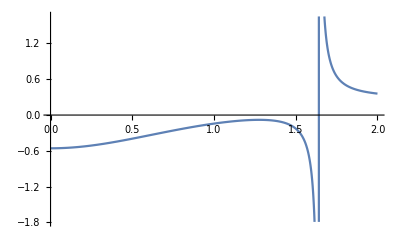

```mathematica
Plot[ascat[1.0,2.0,g,.0001,.05],{g,0,2}]
```

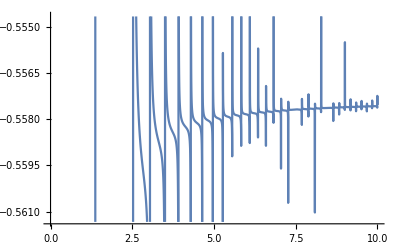

```mathematica
Plot[ascat[1.0,2.0,.1,0.001,ν2],{ν2,0,10}]
```

### Scattering theory basics

Let r be the relative vector from molecule 1 to molecule 2.  Let p denote the internal state of the “projectile” and t describe the “target”. Let J_p be the angular momentum of the projectile and J_t be the angular momentum of the target, and L be the relative angular momentum of the two particles.  There are two different coupling schemes that are possible:

“S basis”:   S=J_p+J_t, and J_tot=L+S

“J basis”:   J_a=L+J_t, and J_a+J_p=J_tot

Asymptotically, when r>> r_0, with both the projectile and target in the ro-vibrational ground state, we expect J_p=J_t=0 and thus S=0 and J_tot=L.  Or, in the J basis, J_a=J_tot=L.  We further let α={p t; J_p J_t S L J_tot} denote all relevant quantum numbers in the S basis and β={p t; J_t L J_a J_p J_tot} be the analogous index in the J basis.

We can write the asymptotic wavefunction as:

The basic formulas for multichannel scattering (See Taylor section 17d).  The partial wave multichannel scattering amplitude is defined as:

f_(α', α)^l=(s_(α', α)^l-δ_(α', α))/(2 ⅈ √(p_α' p_α))

where, p_α=√(2μ_α(E-E_α^th)).  With this definition, the full scattering amplitude is

f(p',α' ←p,α)=∑_L (2L+1)f_(α', α)^l P_l(cos θ)

With only one channel open channel,

s_(1,1)^L=ⅇ^(2ⅈ δ_L)

## Generalize to N channels...

Let’s imagine a two-body Hamiltonian in relative coordinates that is of the form:

H=T+V

V=(V_11 | V_12 | V_13 | ⋯
V_21 | V_22 | V_23 | ⋯
V_31 | V_32 | V_33 | ⋯
⋮ | ⋮ | ⋮ | ⋱)

## scratch...

```mathematica
Clear[k]
```

```mathematica
ψphys=({{ⅇ^(ⅈ k r)S-ⅇ^(-ⅈ k r)}, {n ⅇ^(-q r)}})
```

{{-ⅇ^(-ⅈ k r)+ⅇ^(ⅈ k r) S},{ⅇ^(-q r) n}}

```mathematica
FullSimplify[D[ψphys,r]]
```

{{ⅈ ⅇ^(-ⅈ k r) k (1+ⅇ^(2 ⅈ k r) S)},{-ⅇ^(-q r) n q}}

```mathematica
SphericalBesselK[L_,z_]:=√(π/(2z))BesselK[L+1/2,z]
```

```mathematica
Simplify[FunctionExpand[x SphericalBesselK[0,x]],Assumptions->{x>0}]
```

(ⅇ^-x π)/2

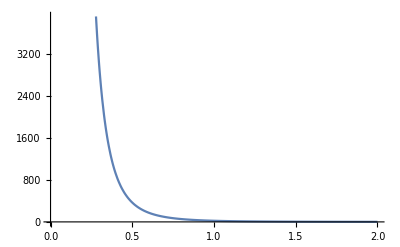

```mathematica
Plot[SphericalBesselK[3,x],{x,0,2}]
```

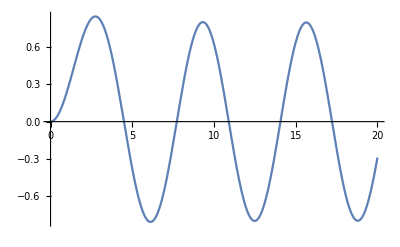

```mathematica
Plot[FullSimplify[FunctionExpand[√x BesselJ[L+1/2,x],Assumptions->{L∈Integers,L>0}]]/.L->1,{x,0,20}]
```